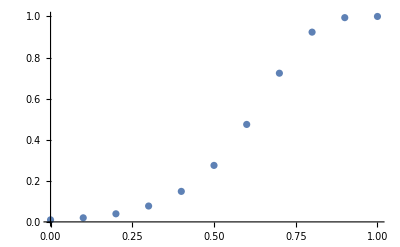

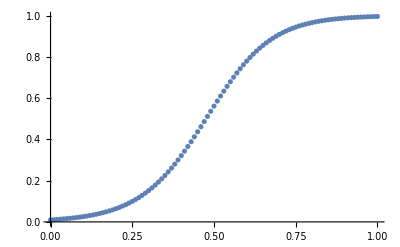

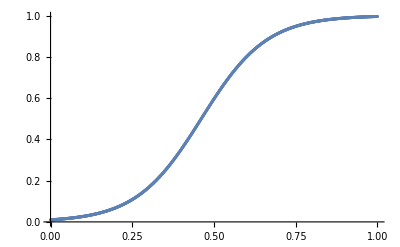

```mathematica
EulerExplicit[f_,t0_,x0_,T_,h_]:=(
n=Ceiling[(T-t0)/h];
t=Table[t0+k*h,{k,0,n}];
x=Table[0,n+1];
x[[1]]=x0;
For[k=1,k≤n,k++,
x[[k+1]]=x[[k]]+h*f[t[[k]],x[[k]]];
];
{t,x}
)


(*Задача*)

f[t_,u_]=10*u*(1-u);
x0=0.01;
t0=0;
T=1;
h1=0.1;
h2=0.01;
h3=0.001;
sol1=EulerExplicit[f,t0,x0,T,h1];
sol2=EulerExplicit[f,t0,x0,T,h2];
sol3=EulerExplicit[f,t0,x0,T,h3];
n1=Length[sol1[[1]]];
n2=Length[sol2[[1]]];
n3=Length[sol3[[1]]];
ListPlot[Table[{sol1[[1]][[k]],sol1[[2]][[k]]},{k,1,n1}]]
ListPlot[Table[{sol2[[1]][[k]],sol2[[2]][[k]]},{k,1,n2}]]
ListPlot[Table[{sol3[[1]][[k]],sol3[[2]][[k]]},{k,1,n3}]]
```